```mathematica
AllData=Import["D:\\Git\\F-Praktikum\\NMR\\Data-Plots\\05-phasenraum-AM-1500Hz-minmax.dat"];
```

```mathematica
xData=Table[0,{n,14,Length[AllData]}];
Do[xData[[n-13]]=AllData[[n,2]],{n,14,Length[AllData]}]
```

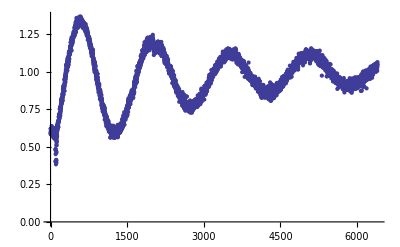

```mathematica
ListPlot[xData]
```

```mathematica
l=1;k=1;
```

```mathematica
Manipulate[ListPlot[Abs[xData^2*l/k^2-2*xData/k*l], PlotRange->{0,10}],{k,-2,2},{l,0.1,50}]
```

ListPlot::lpn: Abs[4.27481\ xData + 3.26321\ xData^2] is not a list of numbers or pairs of numbers.

```mathematica
Manipulate[ListPlot[Abs[((xData/k-1)^2-1)*l], PlotRange->{0,10}],{k,-2,2},{l,0.1,50}]
```

ListPlot::lpn: 10\ Abs[-1 + (-1 - 1.5625\ xData)^2] is not a list of numbers or pairs of numbers.